```mathematica
Directory[]
```

/Users/gasper

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/gasper/Desktop/FMF-vaje/ROM

```mathematica
podatki = Import["rezultati.xlsx", "Dataset", "HeaderLines" -> 1] // First
```

```mathematica
Imena[podatki_] := podatki // Keys // First // Normal
```

```mathematica
Imena[podatki]
```

{Priimek,Ime,Skupina,Točke}

```mathematica
Podatki[podatki_] := podatki // Values// Normal
```

```mathematica
Podatki[podatki]
```

{{Furlan,Luka,A,93.},{Karakaš,Alenka,A,94.},{Kočar,Petra,B,44.},{Kofol,Andraž,C,34.},{Kumar,Barbara,B,67.},{Logar,Mateja,A,42.},{Pance,Martin,B,64.},{Pleterski,Vesna,C,30.},{Trček,Valerija,B,70.},{Virant,Primož,C,58.},{Vesel,Polona,C,66.},{Žveglič,Katarina,A,46.},{Cvelbar,Janja,B,39.},{Furlan,Aleš,B,36.},{Iskra,Sabina,A,77.},{Jerman,Katja,B,100.},{Karničar,Jaka,C,26.},{Korošec,Kristina,B,86.},{Kržišnik,Grega,B,90.},{Obrenović,Tatjana,C,44.},{Puncer,Primož,A,57.},{Ribnikar,Matjaž,A,43.},{Štemberger,Igor,B,85.},{Šubašič,Matej,C,76.},{Tekavčič,Aleksander,A,34.},{Tratnik,Mojca,B,79.},{Smrekar,Andreja,A,38.},{Bezek,Tomaž,B,38.}}

```mathematica
IndeksStolpca[podatki_, stolpec_] := Module[{res}, 
res = Position[Imena[podatki], stolpec];
If[Length[res] == 0, Null, res[[1, 1]]]]

IndeksStolpca[podatki, "Imena"]
```

```mathematica
(Podatki[podatki] // Transpose)[[IndeksStolpca[podatki, "Ime"]]]
```

```mathematica
Stolpec[podatki_, stolpec_] := (Podatki[podatki] // Transpose)[[IndeksStolpca[podatki, stolpec]]]
```

```mathematica
Stolpec[podatki, "Ime"];
```

```mathematica
PovprecjeTock[podatki_] := Stolpec[podatki, "Točke"] // Mean
```

```mathematica
PovprecjeTock[podatki]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_, stolpec_] := Stolpec[podatki, stolpec] // Union
```

```mathematica
RazlicneVrednosti[podatki, "Skupina"]
```

{A,B,C}

```mathematica
Vrstica[podatki_, i_] := Podatki[podatki][[i]]
```

```mathematica
Vrstica[podatki, 2]
```

{Karakaš,Alenka,A,94.}

```mathematica
OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_] := 
If[tocke < za6, 0, 
If[tocke < za7,6,
If[tocke < za8, 7, 
If[tocke < za9, 8, 
If[tocke < za10, 9, 10]]]]]
(* alternativa *)
OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_] := Module[{},
If[tocke < za6, Return 0];
If[tocke < za7, Return 6];
If[tocke < za8, Return 7];
If[tocke < za9, Return 8];
If[tocke < za10, Return 9];
10
]
```

```mathematica
meje = {50, 60, 70, 80, 90};
```

```mathematica
OcenaZaMeje[meje, 50]
```

6

```mathematica
Ocene[podatki_, meje_] := OcenaZaMeje[meje, #] &/@ Stolpec[podatki, "Točke"]
```

```mathematica
Ocene[podatki, meje]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
DodajStolpec[podatki_] := podatki // Query[All, <|#, "Ocena" ->  OcenaZaMeje[meje, #Točke]|> &]
```

```mathematica
podatkiOcene = DodajStolpec[podatki]
```

```mathematica
Export["ocene.xlsx", podatkiOcene]
```

ocene.xlsx

```mathematica
BinCounts[Ocene[podatki, meje]]
```

{0,13,0,0,0,0,0,2,3,4,2,4}

```mathematica
porazdelitevOcen = Drop[Rest[BinCounts[Ocene[podatki, meje]]], {2, 6}]
```

{13,2,3,4,2,4}

```mathematica
BarChart[porazdelitevOcen, 
ChartStyle-> "Rainbow",
PlotLabel->"Ocene pri pisnem izpitu",
Frame -> True,
FrameLabel->{"Število rezultatov", "Ocena"},
ChartLabels->["Negativno", 6, 7, 8, 9, 10]
]
```

```mathematica
IndeksStolpca[podatki_, stolpec_] := Module[{res},
res =Position[Imena[podatki], stolpec];
If[Length[res] == 0, Null, res[[1,1]]]
]
```

```mathematica
IndeksStolpca[podatki, "Ime"]
```

2

```mathematica
IndeksStolpca[podatki, "Neki"]
```

```mathematica
Stolpec[podatki_, stolpec_] := Podatki[podatki] // 
							Transpose // 
							(#[[IndeksStolpca[podatki, stolpec]]])&
```

```mathematica
Stolpec[podatki, "Ime"]
```

{Luka,Alenka,Petra,Andraž,Barbara,Mateja,Martin,Vesna,Valerija,Primož,Polona,Katarina,Janja,Aleš,Sabina,Katja,Jaka,Kristina,Grega,Tatjana,Primož,Matjaž,Igor,Matej,Aleksander,Mojca,Andreja,Tomaž}

```mathematica
Stolpec[podatki, "Točke"]
```

{93.,94.,44.,34.,67.,42.,64.,30.,70.,58.,66.,46.,39.,36.,77.,100.,26.,86.,90.,44.,57.,43.,85.,76.,34.,79.,38.,38.}

```mathematica
PovprecjeTock[podatki_] := Stolpec[podatki, "Točke"] // Mean
```

```mathematica
PovprecjeTock[podatki]
```

59.1429

```mathematica
RazlicneVrednosti[podatki_, stolpec_] := Stolpec[podatki, stolpec] // Union
```

```mathematica
RazlicneVrednosti[podatki, "Skupina"]
```

{A,B,C}

```mathematica
Vrstica[podatki_, i_] := Podatki[podatki][[i]]
```

```mathematica
Vrstica[podatki, 1]
```

{Furlan,Luka,A,93.}

```mathematica
Vrstica[podatki, 2]
```

{Karakaš,Alenka,A,94.}

```mathematica
OcenaZaMeje[{za6_, za7_, za8_, za9_, za10_}, tocke_] := Module[{},
If[tocke ≥ za10, Return[10]];
If[tocke ≥ za9, Return[9]];
If[tocke ≥ za8, Return[8]];
If[tocke ≥ za7, Return[7]];
If[tocke ≥ za6, Return[6]];
0
]
```

```mathematica
meje = {50, 60, 70, 80, 90}
```

{50,60,70,80,90}

```mathematica
OcenaZaMeje[meje, 73]
```

8

```mathematica
OcenaZaMeje[meje, 49]
```

0

```mathematica
OcenaZaMeje[meje, 50]
```

6

```mathematica
Ocene[podatki_, meje_] := OcenaZaMeje[meje, #] & /@Stolpec[podatki, "Točke"]
```

```mathematica
ocene = Ocene[podatki, meje]
```

{10,10,0,0,7,0,7,0,8,6,7,0,0,0,8,10,0,9,10,0,6,0,9,8,0,8,0,0}

```mathematica
DodajStolpec[podatki_, ime_, podStolpec_] := 
podatki // Query[All, <|#, "Ocena" -> OcenaZaMeje[meje, #Točke]|> &]
```

```mathematica
podatkiOcene =DodajStolpec[podatki, "Ocena", Ocene[podatki, meje]]
Export["ocene.xlsx", podatkiOcene]
```

ocene.xlsx

```mathematica
BinCounts[Ocene[podatki, meje]]
```

{0,13,0,0,0,0,0,2,3,4,2,4}

```mathematica
porazdelitevOcen = Drop[BinCounts[Ocene[podatki, meje]]//Rest, {2, 6}]
```

{13,2,3,4,2,4}

```mathematica
napisi = {"Negativno", 6,7,8,9,10}
```

{Negativno,6,7,8,9,10}

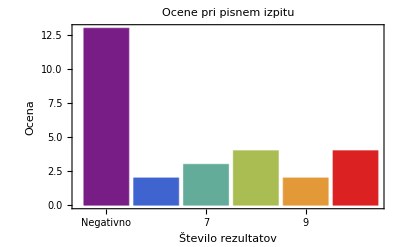

```mathematica
BarChart[porazdelitevOcen, 
ChartStyle->"Rainbow",
ChartLabels->napisi,
Frame-> True,
FrameLabel->{"Število rezultatov", "Ocena"},
PlotLabel -> "Ocene pri pisnem izpitu"
]
```

```mathematica
Export["stolpicni.pdf", %]
```

stolpicni.pdf

```mathematica
delezi = porazdelitevOcen / Sum[porazdelitevOcen[[i]], {i, 1, Length[porazdelitevOcen]}]*100 //N;
(* alternativno *)
delezi = porazdelitevOcen / (Length[Transpose[podatki][[1]]] - 1)*100 //N
```

{48.1481,7.40741,11.1111,14.8148,7.40741,14.8148}

```mathematica
zdruzi[napis_, delez_] := StringJoin[ToString[napis], " (", ToString[DecimalForm[delez,{3,1}]], "%)"]
```

```mathematica
napisi2 = MapThread[zdruzi, {napisi, delezi}]
```

{Negativno (48.1%),6 (7.4%),7 (11.1%),8 (14.8%),9 (7.4%),10 (14.8%)}

```mathematica
PieChart3D[porazdelitevOcen, 
ChartStyle->"Rainbow",
ChartLabels->napisi2,
PlotLabel -> "Ocene pri pisnem izpitu"
]
```

-Graphics3D-

```mathematica
Export["piechart.pdf", %]
```

piechart.pdf

```mathematica
podatkiOcene
```

```mathematica
Vrednost[podatki_, vrstica_, ime_] := vrstica[[IndeksStolpca[podatki, ime]]]
Vrednost[podatkiOcene, Vrstica[podatkiOcene, 2], "Ocena"]
```

10

```mathematica
UstrezaPogoju[podatki_, vrstica_, stolpec_, primerjava_, vrednost_] := primerjava[Vrednost[podatki, vrstica, stolpec],vrednost]
```

```mathematica
v1 =Vrstica[podatkiOcene, 2]
v2 = Vrstica[podatkiOcene, 3]
UstrezaPogoju[podatkiOcene, v1,"Ocena",Equal, 10]
UstrezaPogoju[podatkiOcene, v2,"Ocena", Equal, 10]
```

{Karakaš,Alenka,A,94.,10}

{Kočar,Petra,B,44.,0}

True

False

```mathematica
IzberiVrstice[podatki_, stolpec_, primerjava_, vrednost_] := 
Select[Podatki[podatki], UstrezaPogoju[podatki, #,stolpec, primerjava, vrednost]&] //
Prepend[#, Imena[podatki]]&
```

```mathematica
IzberiVrstice[podatkiOcene, "Ocena", Equal, 9] // TableForm
```

Priimek | Ime | Skupina | Točke | Ocena
Korošec | Kristina | B | 86. | 9
Štemberger | Igor | B | 85. | 9

```mathematica
IzberiVrstice[podatkiOcene, "Ocena", GreaterEqual, 9] // TableForm
```

Priimek | Ime | Skupina | Točke | Ocena
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Jerman | Katja | B | 100. | 10
Korošec | Kristina | B | 86. | 9
Kržišnik | Grega | B | 90. | 10
Štemberger | Igor | B | 85. | 9

```mathematica
IzberiVrstice[podatkiOcene, "Skupina", Equal, "A"]//TableForm
```

Priimek | Ime | Skupina | Točke | Ocena
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Logar | Mateja | A | 42. | 0
Žveglič | Katarina | A | 46. | 0
Iskra | Sabina | A | 77. | 8
Puncer | Primož | A | 57. | 6
Ribnikar | Matjaž | A | 43. | 0
Tekavčič | Aleksander | A | 34. | 0
Smrekar | Andreja | A | 38. | 0

```mathematica
IzberiVrstice[podatkiOcene, "Skupina", Equal, "A"]  //TableForm
```

Priimek | Ime | Skupina | Točke | Ocena
Furlan | Luka | A | 93. | 10
Karakaš | Alenka | A | 94. | 10
Logar | Mateja | A | 42. | 0
Žveglič | Katarina | A | 46. | 0
Iskra | Sabina | A | 77. | 8
Puncer | Primož | A | 57. | 6
Ribnikar | Matjaž | A | 43. | 0
Tekavčič | Aleksander | A | 34. | 0
Smrekar | Andreja | A | 38. | 0

```mathematica
PovprecjeZaSkupino[podatki_, skupina_] := podatki // Query[Select[#Skupina == skupina &] , "Ocena"] // Normal // Mean
```

```mathematica
PovprecjeZaSkupino[podatkiOcene, "A"]
```

34/9

```mathematica
skupine =RazlicneVrednosti[podatkiOcene, "Skupina"];
povprecjaPoSkupinah =Map[PovprecjeZaSkupino[podatkiOcene, #]&, skupine] //N
```

{3.77778,5.66667,3.}

```mathematica
Udelezba[podatki_, skupina_] := podatki // Query[Select[#Skupina == skupina &]] // Values // Length
```

```mathematica
Udelezba[podatkiOcene, "A"]
```

9

```mathematica
Pozitivni[podatki_, skupina_] := podatki // Query[Select[#Ocena >= 6 && #Skupina == skupina&]] // Values // Length
```

```mathematica
Pozitivni[podatkiOcene, "A"]
```

4

```mathematica
udelezbe = Map[Udelezba[podatkiOcene, #]&, skupine]
```

{9,12,7}

```mathematica
pozitivni = Map[Pozitivni[podatkiOcene, #]&, skupine]
```

{4,8,3}

```mathematica
delezi = Map[DecimalForm[#, {3,1}]&,pozitivni/udelezbe*100//N]
delezi = Map[StringJoin[ToString[#], "%"]&, delezi]
```

{44.4,66.7,42.9}

{44.4%,66.7%,42.9%}

```mathematica
povzetek ={skupine, udelezbe, pozitivni, delezi};
povzetek // TableForm
```

A | B | C
9 | 12 | 7
4 | 8 | 3
44.4% | 66.7% | 42.9%

```mathematica
povzetek2 = Transpose[povzetek] // 
Prepend[#, {"", "Udeležba", "Opravili", "Uspešnost"}]&//
  Transpose;
povzetek2// TableForm
```

| A | B | C
Udeležba | 9 | 12 | 7
Opravili | 4 | 8 | 3
Uspešnost | 44.4% | 66.7% | 42.9%

```mathematica
Export["tabela2.pdf", povzetek2// TableForm]
```

tabela2.pdf

```mathematica
Export["Povzetek.xlsx", povzetek2]
```

Povzetek.xlsx